```mathematica
Bezier curves
Definitions
```

```mathematica
Generic Bezier curve equation (of n-th order) with n control points pts.
```

```mathematica
bez [t_,pts_] := Module[ 
{n = Length[pts]-1},
Sum[ Binomial[n,i]If[(n-i)==0And (1-t)==0,1,(1-t)^(n-i)]If[i ==0 And t ==0, 1,t^i]pts[[i+1]], {i,0,n}]
]
```

```mathematica
Parametric plot of a Bezier curve showing the curve and the control points :
```

```mathematica
plotBezier[pts_] :=Show[ParametricPlot[bez[t,pts],{t,0,1}, PlotStyle ->{Thick,Blue}], ListLinePlot[pts, PlotStyle -> {Red,Dashed}, PlotMarkers->"●",AspectRatio->1], PlotRange->All,Axes->False]
```

```mathematica
Find the t's that are solution for the given point p on the Bezier curve defined by the control points pts.
If the point p is not part of the curve, the resulting list will be empty.
```

```mathematica
solveBezierT[p_,pts_] :=Solve[p ==  bez[t,pts],t]
```

```mathematica
Find numPoint points on the Bezier curve defined by the control points pts equally distributed over the t interval
```

```mathematica
pointsOnBezier[numPoints_,pts_]:=Table[bez[t,pts],{t,0,1,1/ numPoints}]
```

```mathematica
Examples
```

```mathematica
pts := {{100,500},{25,400},{475,400},{400,500}};
```

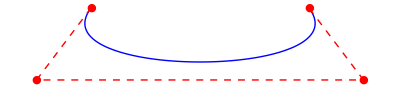

```mathematica
plotBezier[pts]
```

```mathematica
solveBezierT[{100,500},pts]
```

{{t→0}}

```mathematica
quadraticBezier =bez[t, {{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}]
```

{(1-t)^2 x_1+2 (1-t) t x_2+t^2 x_3,(1-t)^2 y_1+2 (1-t) t y_2+t^2 y_3}

```mathematica
cubicBezier =bez[t, {{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}]
```

{(1-t)^3 x_1+3 (1-t)^2 t x_2+3 (1-t) t^2 x_3+t^3 x_4,(1-t)^3 y_1+3 (1-t)^2 t y_2+3 (1-t) t^2 y_3+t^3 y_4}

```mathematica
pb =pointsOnBezier[10,pts]
```

{{100,500},{461/5,473},{548/5,452},{1459/10,437},{974/5,428},{250,425},{1526/5,428},{3541/10,437},{1952/5,452},{2039/5,473},{400,500}}

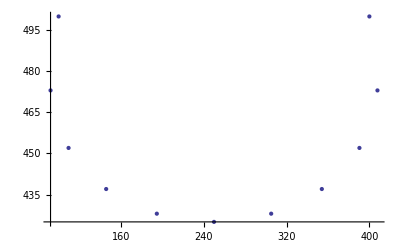

```mathematica
ListPlot[pb]
```